### Introduction

This Mathematica notebook is licensed under a  .

It provides software for producing the endograph of finite functions.   gives a definition of endograph.

The notebook is still rough and incomplete.  It will be revised from time to time.  I hope anyone interested will feel free to improve this work and to use it in their own publications and coursework.

### Definitions

```mathematica
SetOptions[Plot, AspectRatio -> Automatic]; 
tf := TableForm; tx := TeXForm; hh := Hold; 
  ss := Simplify; 
tt[x_] :=TraditionalForm[x]; 
  mf := MatrixForm;
```

```mathematica
RuleGraph[r_]:=GraphPlot[r,VertexLabeling->True, DirectedEdges->True,EdgeRenderingFunction->(Arrow[#1,0.1]&),PlotStyle->{Directive[Arrowheads[0.02]],Thickness[0.003]},VertexRenderingFunction->(Text[Style[#2,16,Bold],#1]&),ImageSize->Large]
```

```mathematica
RuleGraph[r_,gstyle_,n_,arhs_]:=gstyle[r,VertexLabeling->True,DirectedEdges->True,EdgeRenderingFunction->(Arrow[#1,0.2]&),PlotStyle->{Directive[Arrowheads[arhs]],Thickness[0.005]},VertexRenderingFunction->(Text[Style[#2,16,Bold],#1]&),ImageSize->n]
```

```mathematica
ShowGraph[r_,coords_,n_,arhs_]:=GraphPlot[r,VertexCoordinateRules->coords,VertexLabeling->True,DirectedEdges->True,EdgeRenderingFunction->(Arrow[#1,0.2]&),PlotStyle->{Directive[Arrowheads[arhs]],Thickness[0.004]},VertexRenderingFunction->(Text[Style[#2,16,Bold],#1]&),ImageSize->n]
```

```mathematica
Endograph[f_,n_]:=GraphPlot[MakeFunctionRule[f,n],VertexLabeling->True,DirectedEdges->True,EdgeRenderingFunction->(Arrow[#1,0.1]&),PlotStyle->{Directive[Arrowheads[0.02]],Thickness[0.003]},VertexRenderingFunction->(Text[Style[#2,16,Bold],#1]&),ImageSize->Small]
```

```mathematica
LGraph[r_]:=LayeredGraphPlot[r,EdgeRenderingFunction->(Arrow[#1,0.1]&),PlotStyle->{Directive[Arrowheads[0.03]],Thickness[0.003]},VertexRenderingFunction->(Text[Style[#2,16,Bold],#1]&),ImageSize->Small]
```

```mathematica
MakeFunctionRule[f_,n_]:=#->f[#]&/@ Table[k,{k,0,n-1}]
```

```mathematica
FunctionGraph[x_,n_]:=RuleGraph[MakeFunctionRule[x,n]]
```

```mathematica
DFGraph[f_,n_]:=LGraph[MakeFunctionRule[f,n]]
```

### Cograph

This produces cographs only for functions defined on intervals of the form {0, 1, ..., n}

```mathematica
rems[n_]:=Table[i,{i,0,n-1}]
```

```mathematica
rems[5]
```

{0,1,2,3,4}

```mathematica
{#,1}&/@rems[5]
```

{{0,1},{1,1},{2,1},{3,1},{4,1}}

```mathematica
Text[#,{#,1}]&/@rems[5]
```

{Text[0,{0,1}],Text[1,{1,1}],Text[2,{2,1}],Text[3,{3,1}],Text[4,{4,1}]}

```mathematica
Arrow[{{#,1},{#,0}},.2]&/@rems[5]
```

{Arrow[{{0,1},{0,0}},0.2],Arrow[{{1,1},{1,0}},0.2],Arrow[{{2,1},{2,0}},0.2],Arrow[{{3,1},{3,0}},0.2],Arrow[{{4,1},{4,0}},0.2]}

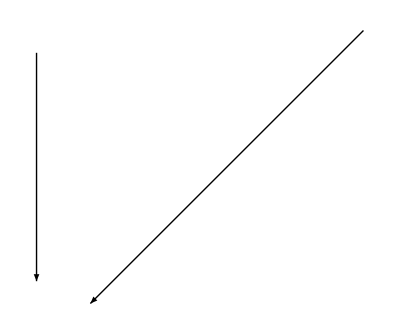

```mathematica
Show[Graphics[{Arrow[{{0,1},{0,0}},0.2],Arrow[{{1,1},{0,0}},0.2]}],ImageSize->Tiny]
```

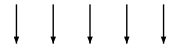

```mathematica
Show[Graphics[{Arrow[{{#,1},{#,0}},.2]&/@rems[5]}],ImageSize->Small]
```

```mathematica
sqf[n_]:=Mod[n^2+1,5]
```

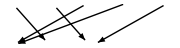

```mathematica
Show[Graphics[{Arrow[{{#,1},{sqf[#],0}},.2]&/@rems[5]}],ImageSize->Small]
```

```mathematica
Show[Graphics[{Arrow[{{#,1},{sqf[#],0}},.2]&/@rems[5]}],ImageSize->Small]
```

-Graphics-

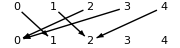

```mathematica
Show[Graphics[{Text[#,{#,1}]&/@rems[5],Text[#,{#,0}]&/@rems[5],Arrow[{{#,1},{sqf[#],0}},.2]&/@rems[5]}],ImageSize->Small]
```

```mathematica
cograph[f_,n_,sb_,is_,ahs_]:=Show[Graphics[{Arrowheads[ahs],Text[#,{#,1}]&/@rems[n],Text[#,{#,0}]&/@rems[n],Arrow[{{#,1},{f[#],0}},sb]&/@rems[n]}],ImageSize->is]
```

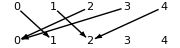

```mathematica
cograph[sqf,5,.15,Small,.04]
```

### Examples

#### fm

```mathematica
fm[n_]:=Mod[n^(11)+n^9+n^7+1,13]
```

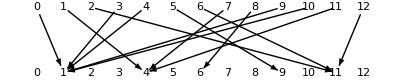

```mathematica
Show[cograph[fm,13,.15,400,.02],AspectRatio->.2]
```

```mathematica
MakeFunctionRule[fm,13]
```

{0→1,1→4,2→11,3→1,4→1,5→9,6→11,7→4,8→6,9→1,10→1,11→4,12→11}

```mathematica
Table[{n,fm[n]},{n,0,12}]
```

{{0,1},{1,4},{2,11},{3,1},{4,1},{5,9},{6,11},{7,4},{8,6},{9,1},{10,1},{11,4},{12,11}}

```mathematica
Table[{n,fm[n]},{n,0,12}]//TableForm
```

0 | 1
1 | 4
2 | 11
3 | 1
4 | 1
5 | 9
6 | 11
7 | 4
8 | 6
9 | 1
10 | 1
11 | 4
12 | 11

```mathematica
Table[{n,fm[n]},{n,0,12}]//TableForm//TeXForm
```

\begin{array}{cc}
 0 & 1 \\
 1 & 4 \\
 2 & 11 \\
 3 & 1 \\
 4 & 1 \\
 5 & 9 \\
 6 & 11 \\
 7 & 4 \\
 8 & 6 \\
 9 & 1 \\
 10 & 1 \\
 11 & 4 \\
 12 & 11 \\
\end{array}

```mathematica
Table[{n,fm[n]},{n,0,12}]//Transpose//TableForm//TeXForm
```

\begin{array}{ccccccccccccc}
 0 & 1 & 2 & 3 & 4 & 5 & 6 & 7 & 8 & 9 & 10 & 11 & 12 \\
 1 & 4 & 11 & 1 & 1 & 9 & 11 & 4 & 6 & 1 & 1 & 4 & 11 \\
\end{array}

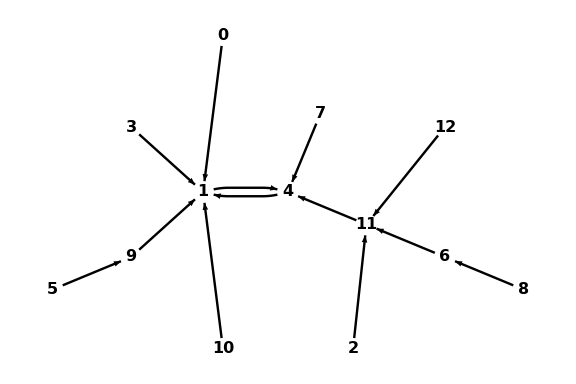

```mathematica
FunctionGraph[fm,13]
```

```mathematica
Table[{n,fm[n]},{n,0,12}]//tf
{{0, 1}, {1, 4}, {2, 11}, {3, 1}, {4, 1}, {5, 9}, {6, 11}, {7, 4}, {8, 6}, {9, 1}, {10, 1}, {11, 4}, {12, 11}}
```

0 | 1
1 | 4
2 | 11
3 | 1
4 | 1
5 | 9
6 | 11
7 | 4
8 | 6
9 | 1
10 | 1
11 | 4
12 | 11

{{0,1},{1,4},{2,11},{3,1},{4,1},{5,9},{6,11},{7,4},{8,6},{9,1},{10,1},{11,4},{12,11}}

```mathematica
{{0,1},{1,4},{2,11},{3,1},{4,1},{5,9},{6,11},{7,4},{8,6},{9,1},{10,1},{11,4},{12,11}}//List//TraditionalForm
```

({0,1} | {1,4} | {2,11} | {3,1} | {4,1} | {5,9} | {6,11} | {7,4} | {8,6} | {9,1} | {10,1} | {11,4} | {12,11})

### Symmetries

#### Square

```mathematica
Show[
Graphics[
{Thick,Point[{{0,0},{0,1},{1,0},{1,1}}]
}
],
ImageSize->50
]
```

-Graphics-

```mathematica
labsty[ch_]=Style[ch,Bold,Larger,Red//Darker]
```

ch

```mathematica
Manipulate[
Show[
Module[
{aa:={0,0},bb:={0,1},cc:={1,0},dd:={1,1}},
Graphics[
{Thick,Point[{aa,bb,cc,dd}],Text[labsty[A],bb+{-e1,e2}],Text[labsty[B],dd+{e1,e2}],Text[labsty[C],cc+{e1,-e2}],Text[labsty[D],aa+{-e1,-e2}]
}
]
],
ImageSize->100
],
{{e1,.1},0,1},{{e2,.1},0,1},AppearanceElements->All
]
```

```mathematica
Manipulate[
Show[
Module[
{aa:={0,0},bb:={0,1},cc:={1,0},dd:={1,1}},
Graphics[
{Thick,Point[{aa,bb,cc,dd}],Text[labsty[A],bb+{-e1,e2}],Text[labsty[B],dd+{e1,e2}],Text[labsty[C],cc+{e1,-e2}],Text[labsty[D],aa+{-e1,-e2}],Line[{aa,bb,dd,cc,aa}]
}
]
],
ImageSize->100
],
{{e1,.1},0,1},{{e2,.1},0,1},AppearanceElements->All
]
```

```mathematica
DiagFlip:=Show[
Module[
{aa:={0,0},bb:={0,1},cc:={1,0},dd:={1,1},aar:={2,0},bbr:={2,1},ccr:={3,0},ddr:={3,1}},
Graphics[
{Thick,Point[{aa,bb,cc,dd}],Text[labsty[A],bb+{-.1,.1}],Text[labsty[B],dd+{.1,.1}],Text[labsty[C],cc+{.1,-.1}],Text[labsty[D],aa+{-.1,-.1}],Line[{aa,bb,dd,cc,aa}],Blue//Darker,Arrowheads[0.05],Arrow[{{1.2,0.5},{1.8,0.5}}],
Black,Point[{aar,bbr,ccr,ddr}],Text[labsty[C],bbr+{-.1,.1}],Text[labsty[B],ddr+{.1,.1}],Text[labsty[A],ccr+{.1,-.1}],Text[labsty[D],aar+{-.1,-.1}],Line[{aar,bbr,ddr,ccr,aar}],Green,Dashed,Line[{aa,dd}]
}
]
],
ImageSize->200
]
```

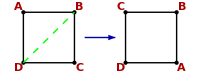

```mathematica
DiagFlip
```

```mathematica
df["A"]="C";df["B"]="B";df["C"]="A";df["D"]="D";
```

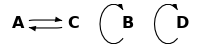

```mathematica
dfgraph=ShowGraph[{"A"->"C","C"->"A","B"->"B","D"->"D"},{"A"->{0,0},"C"->{1,0},"B"->{2,0},"D"->{3,0}},200,.03]
```

```mathematica
gp[ch_,p_]:=Text[Style[ch,Bold],p]
```

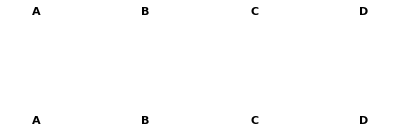

```mathematica
Graphics[{gp["A",{0,1}],gp["A",{0,0}],gp["B",{1,1}],gp["B",{1,0}],gp["C",{2,1}],gp["C",{2,0}],gp["D",{3,1}],gp["D",{3,0}]}]
```

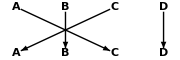

```mathematica
Show[Graphics[{Arrowheads[.05],gp["A",{0,1}],gp["A",{0,0}],gp["B",{1,1}],gp["B",{1,0}],gp["C",{2,1}],gp["C",{2,0}],gp["D",{3,1}],gp["D",{3,0}],Arrow[{{0,1},{2,0}},.1],Arrow[{{2,1},{0,0}},.1],Arrow[{{1,1},{1,0}},.1],Arrow[{{3,1},{3,0}},.1]}],ImageSize->Small]
```

```mathematica
HorizFlip:=Show[
Module[
{aa:={0,0},bb:={0,1},cc:={1,0},dd:={1,1},aar:={2,0},bbr:={2,1},ccr:={3,0},ddr:={3,1}},
Graphics[
{Thick,Point[{aa,bb,cc,dd}],Text[labsty[A],bb+{-.1,.1}],Text[labsty[B],dd+{.1,.1}],Text[labsty[C],cc+{.1,-.1}],Text[labsty[D],aa+{-.1,-.1}],Line[{aa,bb,dd,cc,aa}],Blue//Darker,Arrowheads[0.05],Arrow[{{1.2,0.5},{1.8,0.5}}],
Black,Point[{aar,bbr,ccr,ddr}],Text[labsty[D],bbr+{-.1,.1}],Text[labsty[C],ddr+{.1,.1}],Text[labsty[B],ccr+{.1,-.1}],Text[labsty[A],aar+{-.1,-.1}],Line[{aar,bbr,ddr,ccr,aar}],Green,Dashed,Line[{{0,.5},{1,.5}}]
}
]
],
ImageSize->200
]
```

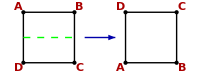

```mathematica
HorizFlip
```

```mathematica
grn:=Green//Darker
```

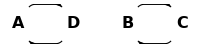

```mathematica
hfgraph=ShowGraph[{"A"->"D","C"->"B","B"->"C","D"->"A"},{"A"->{0,0},"D"->{1,0},"B"->{2,0},"C"->{3,0}},200,.03]
```

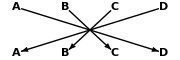

```mathematica
Show[Graphics[{Arrowheads[.05],gp["A",{0,1}],gp["A",{0,0}],gp["B",{1,1}],gp["B",{1,0}],gp["C",{2,1}],gp["C",{2,0}],gp["D",{3,1}],gp["D",{3,0}],Arrow[{{0,1},{3,0}},.1],Arrow[{{1,1},{2,0}},.1],Arrow[{{2,1},{1,0}},.1],Arrow[{{3,1},{0,0}},.1]}],ImageSize->Small]
```

```mathematica
Turn:=Show[
Module[
{aa:={0,0},bb:={0,1},cc:={1,0},dd:={1,1},aar:={2,0},bbr:={2,1},ccr:={3,0},ddr:={3,1}},
Graphics[
{Thick,Point[{aa,bb,cc,dd}],Text[labsty[A],bb+{-.1,.1}],Text[labsty[B],dd+{.1,.1}],Text[labsty[C],cc+{.1,-.1}],Text[labsty[D],aa+{-.1,-.1}],Text[commutative,{0.5,0.5}],Line[{aa,bb,dd,cc,aa}],Blue//Darker,Arrowheads[0.05],Arrow[{{1.2,0.5},{1.8,0.5}}],
Black,Point[{aar,bbr,ccr,ddr}],Text[labsty[B],bbr+{-.1,.1}],Text[labsty[C],ddr+{.1,.1}],Text[labsty[D],ccr+{.1,-.1}],Text[labsty[A],aar+{-.1,-.1}],Line[{aar,bbr,ddr,ccr,aar}]
}
]
],
ImageSize->200
]
```

```mathematica
grn:=Green//Darker
```

```mathematica
commutative=Show[
{ParametricPlot[{Cos[θ],Sin[θ]},{θ,0.6,2 Pi-0.6},PlotRange->{{-1.2,1.4},{-1.3,1.3}},PlotStyle->{grn,Dashed,Thickness[.07]},Axes->False],Graphics[{grn,Thickness[.05],Line[{{.3,.44},{.83,.57},{.82,1.1}}]}]},ImageSize->30]
```

-Graphics-

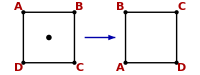

```mathematica
Turn
```

```mathematica
turngraph=ShowGraph[{"A"->"B","B"->"C","C"->"D","D"->"A"},{"A"->{0,1},"B"->{1,1},"D"->{0,0},"C"->{1,0}},66,.13]
```

-Graphics-

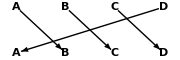

```mathematica
Show[Graphics[{Arrowheads[.05],gp["A",{0,1}],gp["A",{0,0}],gp["B",{1,1}],gp["B",{1,0}],gp["C",{2,1}],gp["C",{2,0}],gp["D",{3,1}],gp["D",{3,0}],Arrow[{{0,1},{1,0}},.1],Arrow[{{1,1},{2,0}},.1],Arrow[{{2,1},{3,0}},.1],Arrow[{{3,1},{0,0}},.1]}],ImageSize->Small]
```